```mathematica
expectedX[0] := 1;
expectedX[2] := x2;
expectedX[4] := (1/(3g))(E0 - 2 x2);
expectedX[u_?EvenQ] := (4 (-3+u) E0 expectedX[(-3+u)-1]+(-3+u) ((-3+u)-1) ((-3+u)-2) expectedX[(-3+u)-3]-4 ((-3+u)+1) expectedX[(-3+u)+1])/(4 g ((-3+u)+2));
expectedX[_?OddQ] := 0;
matPositive[K_] := Table[expectedX[i + j], {i, 0, K}, {j, 0, K}];
FindMinimum[{E0, AllTrue[Eigenvalues[matPositive[11] /. g -> 1], # ≥ 0 &]}, {{x2, 0.307}, {E0, 1.40}}]
```

{1.3922,{x2→0.305782,E0→1.3922}}

说起来，如果只是为了做benchmark，那其实完全可以把所有的表格（基于O和H的对易关系得到的constraint和M矩阵）先列出来再说

```mathematica
normalOrderingRules =  xpOpString[a___, p, x, b___] -> xpOpString[a, x, p, b] - ⅈ xpOpString[a, b];
mulRules = {xpOpString[a___] . xpOpString[b___] -> xpOpString[a, b], 
c_ . xpOpString[a___] /; NumberQ[c] -> c xpOpString[a],
xpOpString[a___] . c_ /; NumberQ[c] -> c xpOpString[a],
a_ . b_ /; NumberQ[a] && NumberQ[b] -> a b};
xntimes[n_] := xpOpString @@ ConstantArray[x, n];
pntimes[n_] := xpOpString @@ ConstantArray[p, n];
xntimes[0] := 1;
pntimes[0] := 1;
xpNormalOrderedOp[xpower_, ppower_] := xntimes[xpower] . pntimes[ppower] /. mulRules;
Lmax = 5;
basisM = Flatten[Table[xpNormalOrderedOp[xpower, ppower], {xpower, 0, Lmax}, {ppower, 0, Lmax}]];
reverseBasisM = Reverse /@ basisM //. {Reverse[1] -> 1};
basislen = Length[basisM];
M = Table[reverseBasisM⟦i⟧ . basisM⟦j⟧ //. mulRules //. normalOrderingRules // Simplify, {i, 1, basislen}, {j, 1, basislen}]
```

Reverse::normal: Reverse[1] 中的位置 1 处应该是非原子表达式.

{{1,xpOpString[p],xpOpString[p,p],xpOpString[p,p,p],xpOpString[p,p,p,p],xpOpString[p,p,p,p,p],xpOpString[x],xpOpString[x,p],20,xpOpString[x,x,x,x,p,p,p,p],xpOpString[x,x,x,x,p,p,p,p,p],xpOpString[x,x,x,x,x],xpOpString[x,x,x,x,x,p],xpOpString[x,x,x,x,x,p,p],xpOpString[x,x,x,x,x,p,p,p],xpOpString[x,x,x,x,x,p,p,p,p],xpOpString[x,x,x,x,x,p,p,p,p,p]},34,{1}}
 |  |  |  |

```mathematica
M⟦1, 36⟧
```

xpOpString[x,x,x,x,x,p,p,p,p,p]

```mathematica
M⟦36, 1⟧
```

-120 ⅈ xpOpString[]+600 xpOpString[x,p]+600 ⅈ xpOpString[x,x,p,p]-200 xpOpString[x,x,x,p,p,p]-25 ⅈ xpOpString[x,x,x,x,p,p,p,p]+xpOpString[x,x,x,x,x,p,p,p,p,p]

```mathematica
reverseBasisM
```

{1,xpOpString[p],xpOpString[p,p],xpOpString[p,p,p],xpOpString[p,p,p,p],xpOpString[p,p,p,p,p],xpOpString[x],xpOpString[p,x],xpOpString[p,p,x],xpOpString[p,p,p,x],xpOpString[p,p,p,p,x],xpOpString[p,p,p,p,p,x],xpOpString[x,x],xpOpString[p,x,x],xpOpString[p,p,x,x],xpOpString[p,p,p,x,x],xpOpString[p,p,p,p,x,x],xpOpString[p,p,p,p,p,x,x],xpOpString[x,x,x],xpOpString[p,x,x,x],xpOpString[p,p,x,x,x],xpOpString[p,p,p,x,x,x],xpOpString[p,p,p,p,x,x,x],xpOpString[p,p,p,p,p,x,x,x],xpOpString[x,x,x,x],xpOpString[p,x,x,x,x],xpOpString[p,p,x,x,x,x],xpOpString[p,p,p,x,x,x,x],xpOpString[p,p,p,p,x,x,x,x],xpOpString[p,p,p,p,p,x,x,x,x],xpOpString[x,x,x,x,x],xpOpString[p,x,x,x,x,x],xpOpString[p,p,x,x,x,x,x],xpOpString[p,p,p,x,x,x,x,x],xpOpString[p,p,p,p,x,x,x,x,x],xpOpString[p,p,p,p,p,x,x,x,x,x]}

```mathematica
H = xntimes[2] + pntimes[2] + xntimes[4];
comm[a_, b_] := ((a . b - b . a) //. mulRules //. normalOrderingRules // TensorExpand // Simplify)  //. mulRules //. normalOrderingRules // Expand
```

```mathematica
basisComm = Flatten[Table[xpNormalOrderedOp[xpower, ppower], {xpower, 0, 2Lmax}, {ppower, 0, 2Lmax}]];
Table[comm[H, basisComm⟦i⟧], {i, 1, Length[basisComm]}]
```

{0,2 ⅈ xpOpString[x]+4 ⅈ xpOpString[x,x,x],1,115,1,10+1,-5040 xpOpString[x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p]-90 xpOpString[x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p,p,p]+5+20 ⅈ xpOpString[x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p,p]+540 xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p]+40 ⅈ xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p,p]}
 |  |  |  |

```mathematica
allXExpected = Table[xpOpString @@ ConstantArray[x, i] -> expectedX[i] /. {g -> 1, x2->0.3057815526686948,E0->1.3921989769203813}, {i, 0, 40}]
```

{xpOpString[]→1,xpOpString[x]→0,xpOpString[x,x]→0.305782,xpOpString[x,x,x]→0,xpOpString[x,x,x,x]→0.260212,xpOpString[x,x,x,x,x]→0,xpOpString[x,x,x,x,x,x]→0.347256,xpOpString[x,x,x,x,x,x,x]→0,xpOpString[x,x,x,x,x,x,x,x]→0.61636,xpOpString[x,x,x,x,x,x,x,x,x]→0,xpOpString[x,x,x,x,x,x,x,x,x,x]→1.34604,xpOpString[x,x,x,x,x,x,x,x,x,x,x]→0,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x]→3.45606,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x]→0,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x]→10.13,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]→0,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]→33.2121,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]→0,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]→119.936,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]→0,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]→471.569,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]→0,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]→2000.71,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]→0,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]→9088.84,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]→0,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]→43946.1,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]→0,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]→225045.,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]→0,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]→1.21476×10^6,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]→0,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]→6.88748×10^6,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]→0,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]→4.08906×10^7,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]→0,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]→2.53363×10^8,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]→0,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]→1.63485×10^9,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]→0,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]→1.09617×10^10}

因此在设置求解变量的时候要特别小心，不能让一些方程从来没有被用过。但是如果设置的求解变量过多，算不出来的期望值就会被写成“不同的期望值之间的关系”。

```mathematica
XnP1Expected = Solve[(# == 0.0)& /@ Table[comm[xntimes[i], H], {i, 1, 40} ] /. allXExpected /. {g -> 1, x2->0.3057815526686948,E0->1.3921989769203813}, Table[(xpOpString @@ ConstantArray[x, n]) . xpOpString[p] //. mulRules, {n, 0, 40}] ]⟦1⟧
```

Solve::svars: 方程可能无法给出所有 " solve " 变量的解.

{xpOpString[p]→0,xpOpString[x,p]→0.+0.5 ⅈ,xpOpString[x,x,p]→0,xpOpString[x,x,x,p]→0.+0.458672 ⅈ,xpOpString[x,x,x,x,p]→0,xpOpString[x,x,x,x,x,p]→0.+0.65053 ⅈ,xpOpString[x,x,x,x,x,x,p]→0,xpOpString[x,x,x,x,x,x,x,p]→0.+1.21539 ⅈ,xpOpString[x,x,x,x,x,x,x,x,p]→0,xpOpString[x,x,x,x,x,x,x,x,x,p]→0.+2.77362 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,p]→0,xpOpString[x,x,x,x,x,x,x,x,x,x,x,p]→0.+7.40324 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,p]→0,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,p]→0.+22.4644 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]→0,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]→0.+75.975 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]→0,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]→0.+282.303 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]→0,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]→0.+1139.39 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]→0,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]→0.+4951.47 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]→0,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]→0.+23008.2 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]→0,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]→0.+113611. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]→0,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]→0.+593273. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]→0,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]→0.+3.26315×10^6 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]→0,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]→0.+1.88287×10^7 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]→0,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]→0.+1.13643×10^8 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]→0,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]→0.+7.15586×10^8 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]→0,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]→0.+4.68722×10^9 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]→0,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]→0.+3.18795×10^10 ⅈ}

```mathematica
XnP2Expected = Solve[Table[0 == comm[xpNormalOrderedOp[i, 1], H], {i, 1, 40} ]/. XnP1Expected /. allXExpected /. {g -> 1, x2->0.3057815526686948,E0->1.3921989769203813}  /. xpOpString[seq__] /; OddQ[Length[{seq}]] -> 0, Table[xpNormalOrderedOp[i, 2], {i, 0, 40}]]⟦1⟧⟦1;;19⟧
```

Solve::svars: 方程可能无法给出所有 " solve " 变量的解.

{xpOpString[p,p]→0.826205+0. ⅈ,xpOpString[x,x,p,p]→-0.181759+0. ⅈ,xpOpString[x,x,x,x,p,p]→-0.601349+0. ⅈ,xpOpString[x,x,x,x,x,x,p,p]→-1.47895+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,p,p]→-3.94401+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,p,p]→-11.7121+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,p,p]→-38.5306+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]→-139.045+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]→-545.267+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]→-2305.31+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]→-10433.+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]→-50249.6+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]→-256337.+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]→-1.37862×10^6+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]→-7.78893×10^6+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]→-4.60869×10^7+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]→-2.84665×10^8+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]→-1.83128×10^9+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]→-1.22438×10^10+0. ⅈ}

```mathematica
XnP3Expected = Solve[Table[0 == comm[xpNormalOrderedOp[i, 2], H], {i, 1, 40} ] /. XnP2Expected/. XnP1Expected/. allXExpected /. {g -> 1, x2->0.3057815526686948,E0->1.3921989769203813}  /. xpOpString[seq__] /; OddQ[Length[{seq}]] -> 0, Table[xpNormalOrderedOp[i, 3], {i, 0, 40}]]⟦1⟧
```

Solve::svars: 方程可能无法给出所有 " solve " 变量的解.

{xpOpString[x,p,p,p]→0.+1.23931 ⅈ,xpOpString[x,x,x,p,p,p]→0.+0.682085 ⅈ,xpOpString[x,x,x,x,x,p,p,p]→0.+0.0766033 ⅈ,xpOpString[x,x,x,x,x,x,x,p,p,p]→0.-1.86789 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,p,p,p]→0.-9.48987 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,p,p,p]→0.-40.7005 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p]→0.-173.895 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p]→0.-769.754 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p]→0.-3571.69 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p]→0.-17427.4 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p]→0.-89368.5 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p]→0.-480889. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p]→0.-2.71018×10^6 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p]→0.-1.59568×10^7 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p]→0.-9.79498×10^7 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p]→0.-6.25678×10^8 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p]→0.-4.14936×10^9 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p]→0.-2.85244×10^10 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p]→(0.-2.26607×10^11 ⅈ)+(0.105263+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p],xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p]→(0.-2.74043×10^8 ⅈ)+(0.+19.5 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]+(0.05+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]-(0.+0.15 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]+(0.1+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]}

```mathematica
XnP4Expected = Solve[Table[0 == comm[xpNormalOrderedOp[i, 3], H], {i, 1, 40} ] /. XnP3Expected /. XnP2Expected/. XnP1Expected/. allXExpected /. {g -> 1, x2->0.3057815526686948,E0->1.3921989769203813}  /. xpOpString[seq__] /; OddQ[Length[{seq}]] -> 0, Table[xpNormalOrderedOp[i, 4], {i, 0, 40}]]⟦1⟧
```

Solve::svars: 方程可能无法给出所有 " solve " 变量的解.

{xpOpString[p,p,p,p]→1.93335+0. ⅈ,xpOpString[x,x,p,p,p,p]→-1.47756+0. ⅈ,xpOpString[x,x,x,x,p,p,p,p]→-3.05202+0. ⅈ,xpOpString[x,x,x,x,x,x,p,p,p,p]→-5.36261+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,p,p,p,p]→-8.18325+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,p,p,p,p]→-3.89309+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p]→61.4837+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p]→513.476+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p]→3240.54+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p]→19202.6+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p]→113142.+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p]→677150.+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p]→4.15559×10^6+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p]→2.62667×10^7+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p]→1.71253×10^8+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p]→1.1524×10^9+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p]→8.004×10^9+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p]→(7.18747×10^10+0. ⅈ)+(0.171429+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p],xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p]→(5.28797×10^11+0. ⅈ)+(0.0810811+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]+(0.162162+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p],xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p]→(4.30461×10^12+0. ⅈ)+(0.0769231+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]+(0.+1.53846 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]+(0.153846+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]}

```mathematica
XnP5Expected = Solve[Table[0 == comm[xpNormalOrderedOp[i, 4], H], {i, 1, 40} ] /. XnP4Expected /. XnP3Expected /. XnP2Expected/. XnP1Expected/. allXExpected /. {g -> 1, x2->0.3057815526686948,E0->1.3921989769203813}  /. xpOpString[seq__] /; OddQ[Length[{seq}]] -> 0, Table[xpNormalOrderedOp[i, 5], {i, 0, 40}]]⟦1⟧
```

Solve::svars: 方程可能无法给出所有 " solve " 变量的解.

{xpOpString[x,p,p,p,p,p]→0.+4.83338 ⅈ,xpOpString[x,x,x,p,p,p,p,p]→0.+1.31136 ⅈ,xpOpString[x,x,x,x,x,p,p,p,p,p]→0.-5.41413 ⅈ,xpOpString[x,x,x,x,x,x,x,p,p,p,p,p]→0.-24.2693 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,p,p,p,p,p]→0.-80.4034 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p]→0.-242.547 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p]→0.-651.351 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p]→0.-1186.15 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p]→0.+2628.57 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p]→0.+54173.5 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p]→0.+499094. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p]→0.+3.92593×10^6 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p]→0.+2.93794×10^7 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p]→0.+2.17268×10^8 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p]→0.+1.61443×10^9 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p]→0.+1.21581×10^10 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p]→(0.+8.76824×10^10 ⅈ)+(0.0247678+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p],xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p]→(0.+1.22844×10^12 ⅈ)+(0.+6.33333 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]+(0.022807+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]-(0.+0.0333333 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]+(0.0222222+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p],xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p]→(0.+9.74297×10^12 ⅈ)+(0.+3.39474 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]+(0.+2.05263 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]+(0.00526316+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]-(0.+0.0157895 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]+(0.210526+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p]+(0.0105263+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p],xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p]→(0.+8.39432×10^13 ⅈ)+(0.+1.35 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]-(31.2+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]+(0.1+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p]+(0.+2.1 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]+(0.2+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p]}

```mathematica
XnP6Expected = Solve[Table[0 == comm[xpNormalOrderedOp[i, 5], H], {i, 1, 40} ] /. XnP5Expected /. XnP4Expected /. XnP3Expected /. XnP2Expected/. XnP1Expected/. allXExpected /. {g -> 1, x2->0.3057815526686948,E0->1.3921989769203813}  /. xpOpString[seq__] /; OddQ[Length[{seq}]] -> 0, Table[xpNormalOrderedOp[i, 6], {i, 0, 40}]]⟦1⟧
```

Solve::svars: 方程可能无法给出所有 " solve " 变量的解.

{xpOpString[p,p,p,p,p,p]→7.2212+0. ⅈ,xpOpString[x,x,p,p,p,p,p,p]→-9.10923+0. ⅈ,xpOpString[x,x,x,x,p,p,p,p,p,p]→-18.9248+0. ⅈ,xpOpString[x,x,x,x,x,x,p,p,p,p,p,p]→-21.9806+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,p,p,p,p,p,p]→19.0191+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p]→291.196+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p]→1638.83+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p]→7699.63+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p]→33358.+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p]→133418.+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p]→454810.+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p]→831933.+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p]→-6.39226×10^6+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p]→-1.13681×10^8+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p]→-1.2274×10^9+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p]→(-6.90741×10^9+0. ⅈ)+(0.0552995+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p],xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p]→(-7.00656×10^10+0. ⅈ)+(0.0505441+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]+(0.04914+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p],xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p]→(-5.41037×10^11+0. ⅈ)+(0.011583+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]+(0.045144+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]+(0.+0.680162 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]+(0.043956+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p],xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p]→(-2.15996×10^13+0. ⅈ)-(85.6216+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]+(0.010395+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]+(0.+0.508896 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]+(0.356757+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]+(0.27027+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p]+(0.02079+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]+(0.+0.237838 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p],xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p]→(-1.85165×10^14+0. ⅈ)-(59.5+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]-(42.0769+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]+(0.+0.0871795 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]+(0.261538+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]+(0.128205+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p]+(0.+2.46154 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p]+(0.+0.174359 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]+(0.25641+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p]}

```mathematica
XnP7Expected = Solve[Table[0 == comm[xpNormalOrderedOp[i, 6], H], {i, 1, 40} ] /. XnP6Expected /. XnP5Expected /. XnP4Expected /. XnP3Expected /. XnP2Expected/. XnP1Expected/. allXExpected /. {g -> 1, x2->0.3057815526686948,E0->1.3921989769203813}  /. xpOpString[seq__] /; OddQ[Length[{seq}]] -> 0, Table[xpNormalOrderedOp[i, 7], {i, 0, 40}]]⟦1⟧
```

Solve::svars: 方程可能无法给出所有 " solve " 变量的解.

{xpOpString[x,p,p,p,p,p,p,p]→0.+25.2742 ⅈ,xpOpString[x,x,x,p,p,p,p,p,p,p]→0.+5.85395 ⅈ,xpOpString[x,x,x,x,x,p,p,p,p,p,p,p]→0.-65.8857 ⅈ,xpOpString[x,x,x,x,x,x,x,p,p,p,p,p,p,p]→0.-245.959 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p]→0.-623.083 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p]→0.-938.236 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p]→0.+2422.99 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p]→0.+35751.8 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p]→0.+261930. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p]→0.+1.61925×10^6 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p]→0.+9.24444×10^6 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p]→0.+4.96282×10^7 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p]→0.+2.45152×10^8 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p]→0.+1.0155×10^9 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p]→(0.-1.51969×10^8 ⅈ)+(0.00990712+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p],xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p]→(0.+1.93661×10^11 ⅈ)+(0.+2.75 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]+(0.0131966+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]-(0.+0.0125 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]+(0.00833333+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p],xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p]→(0.+1.25958×10^12 ⅈ)+(0.+2.85951 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]+(0.+1.10602 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]+(0.00588235+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]-(0.+0.0114551 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]+(0.0743034+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p]+(0.00763674+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p],xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p]→(0.+1.06044×10^13 ⅈ)+(0.+0.734708 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]+(0.+1.32225 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]-(19.1576+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]-(0.+0.00263158 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]+(0.0684211+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p]+(0.+1.08462 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]+(0.00175439+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]+(0.0666667+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p],xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p]→(0.-3.88035×10^14 ⅈ)-(0.+1702.42 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]+(0.+0.375101 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]-(14.0494+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]+(0.+7.54737 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]+(0.+2.63158 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p]+(0.0157895+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p]+(0.+0.655466 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]-(5.03158+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]+(0.315789+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p]+(0.0315789+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p],xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p]→(0.-3.61073×10^15 ⅈ)-(0.+1160.25 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]-(0.+816. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]-(1.7+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]+(0.+5.1 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]+(0.+2.125 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p]-(54.+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p]-(3.4+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]+(0.15+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p]+(0.+2.75 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p]+(0.3+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p]}

```mathematica
XnP8Expected = Solve[Table[0 == comm[xpNormalOrderedOp[i, 7], H], {i, 1, 40} ] /. XnP7Expected /. XnP6Expected /. XnP5Expected /. XnP4Expected /. XnP3Expected /. XnP2Expected/. XnP1Expected/. allXExpected /. {g -> 1, x2->0.3057815526686948,E0->1.3921989769203813}  /. xpOpString[seq__] /; OddQ[Length[{seq}]] -> 0, Table[xpNormalOrderedOp[i, 8], {i, 0, 40}]]⟦1⟧
```

Solve::svars: 方程可能无法给出所有 " solve " 变量的解.

{xpOpString[p,p,p,p,p,p,p,p]→38.0874+0. ⅈ,xpOpString[x,x,p,p,p,p,p,p,p,p]→-58.4308+0. ⅈ,xpOpString[x,x,x,x,p,p,p,p,p,p,p,p]→-179.528+0. ⅈ,xpOpString[x,x,x,x,x,x,p,p,p,p,p,p,p,p]→-117.932+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p]→800.881+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p]→5240.32+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p]→22179.5+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p]→74367.+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p]→162066.+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p]→-322947.+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p]→-7.87765×10^6+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p]→-7.54019×10^7+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p]→-5.90749×10^8+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p]→(-1.79955×10^9+0. ⅈ)+(0.0286738+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p],xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p]→(-1.09864×10^10+0. ⅈ)+(0.0377487+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]+(0.0237228+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p],xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p]→(6.77733×10^9+0. ⅈ)+(0.0166442+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]+(0.0314838+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]+(0.+0.355108 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]+(0.0198511+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p],xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p]→(-8.49254×10^12+0. ⅈ)-(58.3219+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]+(0.013986+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]+(0.+0.468475 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]+(0.224079+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]+(0.11466+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p]+(0.018144+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]+(0.+0.149386 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p],xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p]→(-6.99905×10^13+0. ⅈ)-(74.4879+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]-(30.1874+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]+(0.+0.204019 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]+(0.293861+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]+(0.105336+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p]+(0.+1.48988 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p]+(0.004158+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]+(0.+0.195908 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]+(0.102564+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p],xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p]→(1.91894×10^13+0. ⅈ)-(22.5548+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]-(26.8719+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]-(0.+254.843 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]+(0.0878871+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]+(0.024255+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p]+(0.+1.23725 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p]-(14.1181+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]+(0.+0.0585914 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]+(0.378378+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p]+(0.04851+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p]+(0.+0.518919 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p],xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p]→(7.41787×10^15+0. ⅈ)+(32136.+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]-(6.4+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]-(0.+249.6 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]-(141.785+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]-(60.7692+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p]+(0.+0.246154 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p]-(11.3231+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]-(0.+94.5231 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]+(0.179487+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p]+(0.+2.76923 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p]+(0.+0.492308 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p]+(0.358974+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p]}

```mathematica
XnP9Expected = Solve[Table[0 == comm[xpNormalOrderedOp[i, 8], H], {i, 1, 40} ] /. XnP8Expected /. XnP7Expected /. XnP6Expected /. XnP5Expected /. XnP4Expected /. XnP3Expected /. XnP2Expected/. XnP1Expected/. allXExpected /. {g -> 1,x2->0.3057815526686948,E0->1.3921989769203813}  /. xpOpString[seq__] /; OddQ[Length[{seq}]] -> 0, Table[xpNormalOrderedOp[i, 9], {i, 0, 40}]]⟦1⟧
```

Solve::svars: 方程可能无法给出所有 " solve " 变量的解.

{xpOpString[x,p,p,p,p,p,p,p,p,p]→0.+171.393 ⅈ,xpOpString[x,x,x,p,p,p,p,p,p,p,p,p]→0.+121.055 ⅈ,xpOpString[x,x,x,x,x,p,p,p,p,p,p,p,p,p]→0.-900.886 ⅈ,xpOpString[x,x,x,x,x,x,x,p,p,p,p,p,p,p,p,p]→0.-3199.36 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p,p]→0.-5645.39 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p,p]→0.+7266.96 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p,p]→0.+135994. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p,p]→0.+908431. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p,p]→0.+4.73571×10^6 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p,p]→0.+2.06898×10^7 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p,p]→0.+6.73137×10^7 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p,p]→0.+1.76399×10^7 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p,p]→(0.-3.87906×10^9 ⅈ)+(0.00609669+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p],xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p,p]→(0.+9.53894×10^10 ⅈ)+(0.+1.62673 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]+(0.0103715+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]-(0.+0.00714286 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]+(0.0047619+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p],xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p,p]→(0.+7.22857×10^11 ⅈ)+(0.+2.4711 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]+(0.+0.658671 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]+(0.00665635+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]-(0.+0.00944272 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]+(0.0396285+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p]+(0.00629515+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p],xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p,p]→(0.+6.99266×10^12 ⅈ)+(0.+1.23518 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]+(0.+1.14562 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]-(12.0307+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]-(0.+0.00417957 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]+(0.0527864+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p]+(0.+0.619231 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]+(0.00278638+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]+(0.0333333+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p],xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p,p]→(0.-2.35568×10^14 ⅈ)-(0.+1461.16 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]+(0.+0.629864 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]-(16.2251+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]+(0.+6.14441 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]+(0.+1.79483 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p]+(0.0235294+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p]+(0.+0.724108 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]-(4.09627+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]+(0.148607+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p]+(0.030547+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p],xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p,p]→(0.-2.20446×10^15 ⅈ)-(0.+1914.74 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]-(0.+729.045 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]-(6.74358+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]+(0.+7.88318 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]+(0.+2.56412 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p]-(42.512+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p]+(0.+0.202254 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]-(5.25545+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]+(0.136842+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p]+(0.+1.82051 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p]+(0.00701754+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p]+(0.133333+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p],xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p,p]→(0.-1.65802×10^15 ⅈ)-(0.+617.684 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]-(0.+660.089 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]+(5232.03+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]+(0.+2.50688 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]+(0.+0.801619 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p]-(34.2121+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p]-(0.+294.921 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]-(1.67126+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]+(0.+2.57895 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p]+(0.0315789+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p]+(0.+1.28745 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p]-(13.1368+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p]+(0.421053+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p]+(0.0631579+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p],xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p,p]→(0.+1.44648×10^17 ⅈ)+(0.+626652. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]-(0.+124.8 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]+(4867.2+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]-(0.+2764.8 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]-(0.+1164. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p]-(4.8+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p]-(0.+220.8 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]+(1843.2+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]+(0.+2.8 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p]-(70.8+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p]-(9.6+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p]+(0.2+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p]+(0.+2.8 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p]+(0.4+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p]}

```mathematica
XnP10Expected = Solve[Table[0 == comm[xpNormalOrderedOp[i, 9], H], {i, 1, 40} ] /. XnP9Expected /. XnP8Expected /. XnP7Expected /. XnP6Expected /. XnP5Expected /. XnP4Expected /. XnP3Expected /. XnP2Expected/. XnP1Expected/. allXExpected /. {g -> 1,x2->0.3057815526686948,E0->1.3921989769203813}  /. xpOpString[seq__] /; OddQ[Length[{seq}]] -> 0, Table[xpNormalOrderedOp[i, 10], {i, 0, 40}]]⟦1⟧
```

Solve::svars: 方程可能无法给出所有 " solve " 变量的解.

{xpOpString[p,p,p,p,p,p,p,p,p,p]→290.984+0. ⅈ,xpOpString[x,x,p,p,p,p,p,p,p,p,p,p]→-393.285+0. ⅈ,xpOpString[x,x,x,x,p,p,p,p,p,p,p,p,p,p]→-2602.5+0. ⅈ,xpOpString[x,x,x,x,x,x,p,p,p,p,p,p,p,p,p,p]→-780.606+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p,p,p]→18280.6+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p,p,p]→95736.1+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p,p,p]→311762.+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p,p,p]→493250.+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p,p,p]→-2.79548×10^6+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p,p,p]→-3.80635×10^7+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p,p,p]→-2.95128×10^8+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p,p,p]→(2.20759×10^7+0. ⅈ)+(0.0224404+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p],xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p,p,p]→(3.16394×10^9+0. ⅈ)+(0.0375017+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]+(0.0170804+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p],xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p,p,p]→(8.50779×10^10+0. ⅈ)+(0.0236791+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]+(0.0288968+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]+(0.+0.236738 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]+(0.0132341+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p],xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p,p,p]→(-5.00641×10^12+0. ⅈ)-(40.4082+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]+(0.0184518+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]+(0.+0.435594 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]+(0.14598+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]+(0.0711683+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p]+(0.0174225+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]+(0.+0.0973199 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p],xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p,p,p]→(-4.32615×10^13+0. ⅈ)-(75.7754+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]-(21.2956+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]+(0.+0.298005 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]+(0.282993+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]+(0.0944513+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p]+(0.+0.941791 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p]+(0.00768194+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]+(0.+0.188662 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]+(0.0595533+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p],xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p,p,p]→(-3.72106×10^13+0. ⅈ)-(44.8057+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]-(32.738+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]-(0.+225.694 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]+(0.165234+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]+(0.041958+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p]+(0.+1.39687 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p]-(11.8507+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]+(0.+0.110156 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]+(0.206388+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p]+(0.0544321+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p]+(0.+0.380016 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p],xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p,p,p]→(6.00967×10^15+0. ⅈ)+(33047.6+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]-(17.5335+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]-(0.+376.984 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]-(139.609+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]-(53.3018+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p]+(0.+0.676923 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p]-(17.2015+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]-(0.+93.0729 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]+(0.189605+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p]+(0.+2.00162 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p]+(0.012474+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p]+(0.+0.642463 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p]+(0.184615+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p],xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p,p,p]→(2.46745×10^16+0. ⅈ)+(35334.6+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]+(9420.37+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]-(0.+160.664 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]-(145.749+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]-(49.4627+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p]-(0.+508.386 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p]-(5.75709+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]-(0.+97.166 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]+(0.043659+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p]+(0.+1.95382 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p]-(23.7006+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p]+(0.+0.215341 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p]+(0.486486+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p]+(0.0873181+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p]+(0.+0.648649 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p],xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p,p,p]→(2.49151×10^16+0. ⅈ)+(10665.+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]+(11736.1+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]+(0.+98200.6 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]-(42.9231+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]-(13.2692+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p]-(0.+596.308 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p]+(5522.08+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]-(0.+28.6154 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]-(74.8462+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p]+(0.+0.461538 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p]-(21.9231+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p]-(0.+241.846 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p]+(0.230769+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p]+(0.+2.46154 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p]+(0.+0.923077 ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p]+(0.461538+0. ⅈ) xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p]}

```mathematica
nonzeroExpected = Select[Union[allXExpected, XnP1Expected, XnP2Expected, XnP3Expected, XnP4Expected, XnP5Expected, XnP6Expected, XnP7Expected, XnP8Expected, XnP9Expected, XnP10Expected], (Length[#⟦1⟧] ≤ 20 && #⟦2⟧ ≠ 0)&]
```

{xpOpString[]→1,xpOpString[p,p]→0.826205+0. ⅈ,xpOpString[x,p]→0.+0.5 ⅈ,xpOpString[x,x]→0.305782,xpOpString[p,p,p,p]→1.93335+0. ⅈ,xpOpString[x,p,p,p]→0.+1.23931 ⅈ,xpOpString[x,x,p,p]→-0.181759+0. ⅈ,xpOpString[x,x,x,p]→0.+0.458672 ⅈ,xpOpString[x,x,x,x]→0.260212,xpOpString[p,p,p,p,p,p]→7.2212+0. ⅈ,xpOpString[x,p,p,p,p,p]→0.+4.83338 ⅈ,xpOpString[x,x,p,p,p,p]→-1.47756+0. ⅈ,xpOpString[x,x,x,p,p,p]→0.+0.682085 ⅈ,xpOpString[x,x,x,x,p,p]→-0.601349+0. ⅈ,xpOpString[x,x,x,x,x,p]→0.+0.65053 ⅈ,xpOpString[x,x,x,x,x,x]→0.347256,xpOpString[p,p,p,p,p,p,p,p]→38.0874+0. ⅈ,xpOpString[x,p,p,p,p,p,p,p]→0.+25.2742 ⅈ,xpOpString[x,x,p,p,p,p,p,p]→-9.10923+0. ⅈ,xpOpString[x,x,x,p,p,p,p,p]→0.+1.31136 ⅈ,xpOpString[x,x,x,x,p,p,p,p]→-3.05202+0. ⅈ,xpOpString[x,x,x,x,x,p,p,p]→0.+0.0766033 ⅈ,xpOpString[x,x,x,x,x,x,p,p]→-1.47895+0. ⅈ,xpOpString[x,x,x,x,x,x,x,p]→0.+1.21539 ⅈ,xpOpString[x,x,x,x,x,x,x,x]→0.61636,xpOpString[p,p,p,p,p,p,p,p,p,p]→290.984+0. ⅈ,xpOpString[x,p,p,p,p,p,p,p,p,p]→0.+171.393 ⅈ,xpOpString[x,x,p,p,p,p,p,p,p,p]→-58.4308+0. ⅈ,xpOpString[x,x,x,p,p,p,p,p,p,p]→0.+5.85395 ⅈ,xpOpString[x,x,x,x,p,p,p,p,p,p]→-18.9248+0. ⅈ,xpOpString[x,x,x,x,x,p,p,p,p,p]→0.-5.41413 ⅈ,xpOpString[x,x,x,x,x,x,p,p,p,p]→-5.36261+0. ⅈ,xpOpString[x,x,x,x,x,x,x,p,p,p]→0.-1.86789 ⅈ,xpOpString[x,x,x,x,x,x,x,x,p,p]→-3.94401+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,p]→0.+2.77362 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x]→1.34604,xpOpString[x,x,p,p,p,p,p,p,p,p,p,p]→-393.285+0. ⅈ,xpOpString[x,x,x,p,p,p,p,p,p,p,p,p]→0.+121.055 ⅈ,xpOpString[x,x,x,x,p,p,p,p,p,p,p,p]→-179.528+0. ⅈ,xpOpString[x,x,x,x,x,p,p,p,p,p,p,p]→0.-65.8857 ⅈ,xpOpString[x,x,x,x,x,x,p,p,p,p,p,p]→-21.9806+0. ⅈ,xpOpString[x,x,x,x,x,x,x,p,p,p,p,p]→0.-24.2693 ⅈ,xpOpString[x,x,x,x,x,x,x,x,p,p,p,p]→-8.18325+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,p,p,p]→0.-9.48987 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,p,p]→-11.7121+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,p]→0.+7.40324 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x]→3.45606,xpOpString[x,x,x,x,p,p,p,p,p,p,p,p,p,p]→-2602.5+0. ⅈ,xpOpString[x,x,x,x,x,p,p,p,p,p,p,p,p,p]→0.-900.886 ⅈ,xpOpString[x,x,x,x,x,x,p,p,p,p,p,p,p,p]→-117.932+0. ⅈ,xpOpString[x,x,x,x,x,x,x,p,p,p,p,p,p,p]→0.-245.959 ⅈ,xpOpString[x,x,x,x,x,x,x,x,p,p,p,p,p,p]→19.0191+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,p,p,p,p,p]→0.-80.4034 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,p,p,p,p]→-3.89309+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,p,p,p]→0.-40.7005 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,p,p]→-38.5306+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,p]→0.+22.4644 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x]→10.13,xpOpString[x,x,x,x,x,x,p,p,p,p,p,p,p,p,p,p]→-780.606+0. ⅈ,xpOpString[x,x,x,x,x,x,x,p,p,p,p,p,p,p,p,p]→0.-3199.36 ⅈ,xpOpString[x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p]→800.881+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p]→0.-623.083 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p]→291.196+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p]→0.-242.547 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p]→61.4837+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p]→0.-173.895 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]→-139.045+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]→0.+75.975 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]→33.2121,xpOpString[x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p,p,p]→18280.6+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p,p]→0.-5645.39 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p]→5240.32+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p]→0.-938.236 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p]→1638.83+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p]→0.-651.351 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p]→513.476+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p]→0.-769.754 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]→-545.267+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]→0.+282.303 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]→119.936,xpOpString[x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p,p,p]→95736.1+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p,p]→0.+7266.96 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p,p]→22179.5+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p,p]→0.+2422.99 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p,p]→7699.63+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p,p]→0.-1186.15 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p,p]→3240.54+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p,p]→0.-3571.69 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p,p]→-2305.31+0. ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,p]→0.+1139.39 ⅈ,xpOpString[x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x]→471.569}

```mathematica
Eigenvalues[(M /. nonzeroExpected /. xpOpString[seq__] /; OddQ[Length[{seq}]] -> 0)]
```

{152336.-5.82915×10^-27 ⅈ,35073.5+3.91612×10^-13 ⅈ,7871.89-4.44602×10^-15 ⅈ,3219.71-1.58609×10^-22 ⅈ,1110.89+2.40727×10^-19 ⅈ,418.283+1.2948×10^-13 ⅈ,143.947-7.15215×10^-14 ⅈ,142.996-1.49607×10^-17 ⅈ,34.4983-3.42643×10^-16 ⅈ,25.0739-5.5775×10^-14 ⅈ,10.7244-7.5518×10^-16 ⅈ,1.07144-8.44861×10^-15 ⅈ,0.186934-4.50378×10^-14 ⅈ,0.0251751-1.2993×10^-13 ⅈ,0.0198789+9.43544×10^-14 ⅈ,-0.0059278+8.04763×10^-14 ⅈ,0.00248624-5.08709×10^-16 ⅈ,0.0019754-2.24352×10^-14 ⅈ,-0.00160649-6.91339×10^-15 ⅈ,-0.00122542-7.0869×10^-14 ⅈ,-0.001218+1.213×10^-13 ⅈ,0.000608623-4.56252×10^-14 ⅈ,0.000213875+2.92202×10^-15 ⅈ,0.000120688-3.48763×10^-14 ⅈ,-0.0000893295-9.33791×10^-15 ⅈ,0.0000463036-9.09516×10^-15 ⅈ,-0.0000309406-1.58703×10^-14 ⅈ,-0.0000208805+1.25564×10^-14 ⅈ,7.20595×10^-13+3.29011×10^-15 ⅈ,4.31193×10^-14-2.49651×10^-14 ⅈ,-3.2087×10^-14-1.42441×10^-14 ⅈ,-4.78065×10^-15+3.12017×10^-14 ⅈ,1.02673×10^-14-1.8883×10^-14 ⅈ,9.02898×10^-15+1.00468×10^-14 ⅈ,-1.29958×10^-14-1.67073×10^-15 ⅈ,2.04275×10^-16-1.62585×10^-15 ⅈ}

```mathematica
Eigenvalues[(Table[xpNormalOrderedOp[i + j, 0], {i, 0, 10}, {j, 0, 10}] /. nonzeroExpected /. xpOpString[seq__] /; OddQ[Length[{seq}]] -> 0)]
```

{504.899,130.211,4.0255,1.59372,1.01345,0.236806,0.16176,0.0226981,0.0132164,0.000721841,0.000523045}

```mathematica
Product[Eigenvalues[(M /. nonzeroExpected /. xpOpString[seq__] /; OddQ[Length[{seq}]] -> 0)]⟦i⟧, {i, 1, Length[M]}]
```

-8.73342×10^-127-5.97826×10^-128 ⅈ

```mathematica
complexToMat[complexmat_] := Module[{len = Length[complexmat], res},
res = Table[0, {i, 1, 2 len}, {j, 1, 2len}]; 
For[i = 1, i ≤ len, i ++, 
For[j = 1, j ≤ len, j ++, 
res⟦2i-1, 2j-1⟧ = Re[complexmat⟦i,j⟧];
res⟦2i-1, 2j⟧ = -Im[complexmat⟦i,j⟧];
res⟦2i, 2j-1⟧ = Im[complexmat⟦i,j⟧];
res⟦2i, 2j⟧ = Re[complexmat⟦i,j⟧];
]];
res]
```

```mathematica
complexToMat[(M/.nonzeroExpected/.xpOpString[seq__]/;OddQ[Length[{seq}]]->0)] // MatrixForm
```

(1 | 0 | 0 | 0 | 0.826205 | 0. | 0 | 0 | 1.93335 | 0. | 0 | 0 | 0 | 0 | 0. | -0.5 | 0 | 0 | 0. | -1.23931 | 0 | 0 | 0. | -4.83338 | 0.305782 | 0 | 0 | 0 | -0.181759 | 0. | 0 | 0 | -1.47756 | 0. | 0 | 0 | 0 | 0 | 0. | -0.458672 | 0 | 0 | 0. | -0.682085 | 0 | 0 | 0. | -1.31136 | 0.260212 | 0 | 0 | 0 | -0.601349 | 0. | 0 | 0 | -3.05202 | 0. | 0 | 0 | 0 | 0 | 0. | -0.65053 | 0 | 0 | 0. | -0.0766033 | 0 | 0 | 0. | 5.41413
0 | 1 | 0 | 0 | 0. | 0.826205 | 0 | 0 | 0. | 1.93335 | 0 | 0 | 0 | 0 | 0.5 | 0. | 0 | 0 | 1.23931 | 0. | 0 | 0 | 4.83338 | 0. | 0 | 0.305782 | 0 | 0 | 0. | -0.181759 | 0 | 0 | 0. | -1.47756 | 0 | 0 | 0 | 0 | 0.458672 | 0. | 0 | 0 | 0.682085 | 0. | 0 | 0 | 1.31136 | 0. | 0 | 0.260212 | 0 | 0 | 0. | -0.601349 | 0 | 0 | 0. | -3.05202 | 0 | 0 | 0 | 0 | 0.65053 | 0. | 0 | 0 | 0.0766033 | 0. | 0 | 0 | -5.41413 | 0.
0 | 0 | 0.826205 | 0. | 0 | 0 | 1.93335 | 0. | 0 | 0 | 7.2212 | 0. | 0. | 0.5 | 0 | 0 | 0. | -0.413103 | 0 | 0 | 0. | -2.90003 | 0 | 0 | 0 | 0 | 0.818241 | 0. | 0 | 0 | 1.00105 | 0. | 0 | 0 | 0.557519 | 0. | 0. | 0.458672 | 0 | 0 | 0. | -1.22736 | 0 | 0 | 0. | -5.74405 | 0 | 0 | 0 | 0 | 1.23334 | 0. | 0 | 0 | -0.323684 | 0. | 0 | 0 | -13.6794 | 0. | 0. | 0.65053 | 0 | 0 | 0. | -3.08335 | 0 | 0 | 0. | -9.84599 | 0 | 0
0 | 0 | 0. | 0.826205 | 0 | 0 | 0. | 1.93335 | 0 | 0 | 0. | 7.2212 | -0.5 | 0. | 0 | 0 | 0.413103 | 0. | 0 | 0 | 2.90003 | 0. | 0 | 0 | 0 | 0 | 0. | 0.818241 | 0 | 0 | 0. | 1.00105 | 0 | 0 | 0. | 0.557519 | -0.458672 | 0. | 0 | 0 | 1.22736 | 0. | 0 | 0 | 5.74405 | 0. | 0 | 0 | 0 | 0 | 0. | 1.23334 | 0 | 0 | 0. | -0.323684 | 0 | 0 | 0. | -13.6794 | -0.65053 | 0. | 0 | 0 | 3.08335 | 0. | 0 | 0 | 9.84599 | 0. | 0 | 0
0.826205 | 0. | 0 | 0 | 1.93335 | 0. | 0 | 0 | 7.2212 | 0. | 0 | 0 | 0 | 0 | 0. | 0.413103 | 0 | 0 | 0. | -0.966675 | 0 | 0 | 0. | -10.8318 | -0.181759 | 0. | 0 | 0 | 1.82726 | 0. | 0 | 0 | 6.35757 | 0. | 0 | 0 | 0 | 0 | 0. | 1.22736 | 0 | 0 | 0. | -2.74089 | 0 | 0 | 0. | -31.5091 | -0.601349 | 0. | 0 | 0 | 4.58576 | 0. | 0 | 0 | 9.29684 | 0. | 0 | 0 | 0 | 0 | 0. | 3.08335 | 0 | 0 | 0. | -11.4644 | 0 | 0 | 0. | -97.1352
0. | 0.826205 | 0 | 0 | 0. | 1.93335 | 0 | 0 | 0. | 7.2212 | 0 | 0 | 0 | 0 | -0.413103 | 0. | 0 | 0 | 0.966675 | 0. | 0 | 0 | 10.8318 | 0. | 0. | -0.181759 | 0 | 0 | 0. | 1.82726 | 0 | 0 | 0. | 6.35757 | 0 | 0 | 0 | 0 | -1.22736 | 0. | 0 | 0 | 2.74089 | 0. | 0 | 0 | 31.5091 | 0. | 0. | -0.601349 | 0 | 0 | 0. | 4.58576 | 0 | 0 | 0. | 9.29684 | 0 | 0 | 0 | 0 | -3.08335 | 0. | 0 | 0 | 11.4644 | 0. | 0 | 0 | 97.1352 | 0.
0 | 0 | 1.93335 | 0. | 0 | 0 | 7.2212 | 0. | 0 | 0 | 38.0874 | 0. | 0. | 1.23931 | 0 | 0 | 0. | 0.966675 | 0 | 0 | 0. | -3.6106 | 0 | 0 | 0 | 0 | 1.00105 | 0. | 0 | 0 | 8.29092 | 0. | 0 | 0 | 49.8871 | 0. | 0. | 0.682085 | 0 | 0 | 0. | 2.74089 | 0 | 0 | 0. | -12.4364 | 0 | 0 | 0 | 0 | -0.323684 | 0. | 0 | 0 | 20.2604 | 0. | 0 | 0 | 102.651 | 0. | 0. | 0.0766033 | 0 | 0 | 0. | 11.4644 | 0 | 0 | 0. | -50.651 | 0 | 0
0 | 0 | 0. | 1.93335 | 0 | 0 | 0. | 7.2212 | 0 | 0 | 0. | 38.0874 | -1.23931 | 0. | 0 | 0 | -0.966675 | 0. | 0 | 0 | 3.6106 | 0. | 0 | 0 | 0 | 0 | 0. | 1.00105 | 0 | 0 | 0. | 8.29092 | 0 | 0 | 0. | 49.8871 | -0.682085 | 0. | 0 | 0 | -2.74089 | 0. | 0 | 0 | 12.4364 | 0. | 0 | 0 | 0 | 0 | 0. | -0.323684 | 0 | 0 | 0. | 20.2604 | 0 | 0 | 0. | 102.651 | -0.0766033 | 0. | 0 | 0 | -11.4644 | 0. | 0 | 0 | 50.651 | 0. | 0 | 0
1.93335 | 0. | 0 | 0 | 7.2212 | 0. | 0 | 0 | 38.0874 | 0. | 0 | 0 | 0 | 0 | 0. | 2.90003 | 0 | 0 | 0. | 3.6106 | 0 | 0 | 0. | -19.0437 | -1.47756 | 0. | 0 | 0 | 6.35757 | 0. | 0 | 0 | 57.1083 | 0. | 0 | 0 | 0 | 0 | 0. | 5.74405 | 0 | 0 | 0. | 12.4364 | 0 | 0 | 0. | -85.6625 | -3.05202 | 0. | 0 | 0 | 9.29684 | 0. | 0 | 0 | 152.396 | 0. | 0 | 0 | 0 | 0 | 0. | 9.84599 | 0 | 0 | 0. | 50.651 | 0 | 0 | 0. | -380.991
0. | 1.93335 | 0 | 0 | 0. | 7.2212 | 0 | 0 | 0. | 38.0874 | 0 | 0 | 0 | 0 | -2.90003 | 0. | 0 | 0 | -3.6106 | 0. | 0 | 0 | 19.0437 | 0. | 0. | -1.47756 | 0 | 0 | 0. | 6.35757 | 0 | 0 | 0. | 57.1083 | 0 | 0 | 0 | 0 | -5.74405 | 0. | 0 | 0 | -12.4364 | 0. | 0 | 0 | 85.6625 | 0. | 0. | -3.05202 | 0 | 0 | 0. | 9.29684 | 0 | 0 | 0. | 152.396 | 0 | 0 | 0 | 0 | -9.84599 | 0. | 0 | 0 | -50.651 | 0. | 0 | 0 | 380.991 | 0.
0 | 0 | 7.2212 | 0. | 0 | 0 | 38.0874 | 0. | 0 | 0 | 290.984 | 0. | 0. | 4.83338 | 0 | 0 | 0. | 10.8318 | 0 | 0 | 0. | 19.0437 | 0 | 0 | 0 | 0 | 0.557519 | 0. | 0 | 0 | 49.8871 | 0. | 0 | 0 | 558.9 | 0. | 0. | 1.31136 | 0 | 0 | 0. | 31.5091 | 0 | 0 | 0. | 85.6625 | 0 | 0 | 0 | 0 | -13.6794 | 0. | 0 | 0 | 102.651 | 0. | 0 | 0 | 1631.04 | 0. | 0. | -5.41413 | 0 | 0 | 0. | 97.1352 | 0 | 0 | 0. | 380.991 | 0 | 0
0 | 0 | 0. | 7.2212 | 0 | 0 | 0. | 38.0874 | 0 | 0 | 0. | 290.984 | -4.83338 | 0. | 0 | 0 | -10.8318 | 0. | 0 | 0 | -19.0437 | 0. | 0 | 0 | 0 | 0 | 0. | 0.557519 | 0 | 0 | 0. | 49.8871 | 0 | 0 | 0. | 558.9 | -1.31136 | 0. | 0 | 0 | -31.5091 | 0. | 0 | 0 | -85.6625 | 0. | 0 | 0 | 0 | 0 | 0. | -13.6794 | 0 | 0 | 0. | 102.651 | 0 | 0 | 0. | 1631.04 | 5.41413 | 0. | 0 | 0 | -97.1352 | 0. | 0 | 0 | -380.991 | 0. | 0 | 0
0 | 0 | 0. | -0.5 | 0 | 0 | 0. | -1.23931 | 0 | 0 | 0. | -4.83338 | 0.305782 | 0 | 0 | 0 | -0.181759 | 0. | 0 | 0 | -1.47756 | 0. | 0 | 0 | 0 | 0 | 0. | -0.458672 | 0 | 0 | 0. | -0.682085 | 0 | 0 | 0. | -1.31136 | 0.260212 | 0 | 0 | 0 | -0.601349 | 0. | 0 | 0 | -3.05202 | 0. | 0 | 0 | 0 | 0 | 0. | -0.65053 | 0 | 0 | 0. | -0.0766033 | 0 | 0 | 0. | 5.41413 | 0.347256 | 0 | 0 | 0 | -1.47895 | 0. | 0 | 0 | -5.36261 | 0. | 0 | 0
0 | 0 | 0.5 | 0. | 0 | 0 | 1.23931 | 0. | 0 | 0 | 4.83338 | 0. | 0 | 0.305782 | 0 | 0 | 0. | -0.181759 | 0 | 0 | 0. | -1.47756 | 0 | 0 | 0 | 0 | 0.458672 | 0. | 0 | 0 | 0.682085 | 0. | 0 | 0 | 1.31136 | 0. | 0 | 0.260212 | 0 | 0 | 0. | -0.601349 | 0 | 0 | 0. | -3.05202 | 0 | 0 | 0 | 0 | 0.65053 | 0. | 0 | 0 | 0.0766033 | 0. | 0 | 0 | -5.41413 | 0. | 0 | 0.347256 | 0 | 0 | 0. | -1.47895 | 0 | 0 | 0. | -5.36261 | 0 | 0
0. | 0.5 | 0 | 0 | 0. | -0.413103 | 0 | 0 | 0. | -2.90003 | 0 | 0 | 0 | 0 | 0.818241 | 0. | 0 | 0 | 1.00105 | 0. | 0 | 0 | 0.557519 | 0. | 0. | 0.458672 | 0 | 0 | 0. | -1.22736 | 0 | 0 | 0. | -5.74405 | 0 | 0 | 0 | 0 | 1.23334 | 0. | 0 | 0 | -0.323684 | 0. | 0 | 0 | -13.6794 | 0. | 0. | 0.65053 | 0 | 0 | 0. | -3.08335 | 0 | 0 | 0. | -9.84599 | 0 | 0 | 0 | 0 | 2.42422 | 0. | 0 | 0 | -4.90299 | 0. | 0 | 0 | -54.4654 | 0.
-0.5 | 0. | 0 | 0 | 0.413103 | 0. | 0 | 0 | 2.90003 | 0. | 0 | 0 | 0 | 0 | 0. | 0.818241 | 0 | 0 | 0. | 1.00105 | 0 | 0 | 0. | 0.557519 | -0.458672 | 0. | 0 | 0 | 1.22736 | 0. | 0 | 0 | 5.74405 | 0. | 0 | 0 | 0 | 0 | 0. | 1.23334 | 0 | 0 | 0. | -0.323684 | 0 | 0 | 0. | -13.6794 | -0.65053 | 0. | 0 | 0 | 3.08335 | 0. | 0 | 0 | 9.84599 | 0. | 0 | 0 | 0 | 0 | 0. | 2.42422 | 0 | 0 | 0. | -4.90299 | 0 | 0 | 0. | -54.4654
0 | 0 | 0. | 0.413103 | 0 | 0 | 0. | -0.966675 | 0 | 0 | 0. | -10.8318 | -0.181759 | 0. | 0 | 0 | 1.82726 | 0. | 0 | 0 | 6.35757 | 0. | 0 | 0 | 0 | 0 | 0. | 1.22736 | 0 | 0 | 0. | -2.74089 | 0 | 0 | 0. | -31.5091 | -0.601349 | 0. | 0 | 0 | 4.58576 | 0. | 0 | 0 | 9.29684 | 0. | 0 | 0 | 0 | 0 | 0. | 3.08335 | 0 | 0 | 0. | -11.4644 | 0 | 0 | 0. | -97.1352 | -1.47895 | 0. | 0 | 0 | 13.5971 | 0. | 0 | 0 | 4.61052 | 0. | 0 | 0
0 | 0 | -0.413103 | 0. | 0 | 0 | 0.966675 | 0. | 0 | 0 | 10.8318 | 0. | 0. | -0.181759 | 0 | 0 | 0. | 1.82726 | 0 | 0 | 0. | 6.35757 | 0 | 0 | 0 | 0 | -1.22736 | 0. | 0 | 0 | 2.74089 | 0. | 0 | 0 | 31.5091 | 0. | 0. | -0.601349 | 0 | 0 | 0. | 4.58576 | 0 | 0 | 0. | 9.29684 | 0 | 0 | 0 | 0 | -3.08335 | 0. | 0 | 0 | 11.4644 | 0. | 0 | 0 | 97.1352 | 0. | 0. | -1.47895 | 0 | 0 | 0. | 13.5971 | 0 | 0 | 0. | 4.61052 | 0 | 0
0. | 1.23931 | 0 | 0 | 0. | 0.966675 | 0 | 0 | 0. | -3.6106 | 0 | 0 | 0 | 0 | 1.00105 | 0. | 0 | 0 | 8.29092 | 0. | 0 | 0 | 49.8871 | 0. | 0. | 0.682085 | 0 | 0 | 0. | 2.74089 | 0 | 0 | 0. | -12.4364 | 0 | 0 | 0 | 0 | -0.323684 | 0. | 0 | 0 | 20.2604 | 0. | 0 | 0 | 102.651 | 0. | 0. | 0.0766033 | 0 | 0 | 0. | 11.4644 | 0 | 0 | 0. | -50.651 | 0 | 0 | 0 | 0 | -4.90299 | 0. | 0 | 0 | 73.397 | 0. | 0 | 0 | 241.994 | 0.
-1.23931 | 0. | 0 | 0 | -0.966675 | 0. | 0 | 0 | 3.6106 | 0. | 0 | 0 | 0 | 0 | 0. | 1.00105 | 0 | 0 | 0. | 8.29092 | 0 | 0 | 0. | 49.8871 | -0.682085 | 0. | 0 | 0 | -2.74089 | 0. | 0 | 0 | 12.4364 | 0. | 0 | 0 | 0 | 0 | 0. | -0.323684 | 0 | 0 | 0. | 20.2604 | 0 | 0 | 0. | 102.651 | -0.0766033 | 0. | 0 | 0 | -11.4644 | 0. | 0 | 0 | 50.651 | 0. | 0 | 0 | 0 | 0 | 0. | -4.90299 | 0 | 0 | 0. | 73.397 | 0 | 0 | 0. | 241.994
0 | 0 | 0. | 2.90003 | 0 | 0 | 0. | 3.6106 | 0 | 0 | 0. | -19.0437 | -1.47756 | 0. | 0 | 0 | 6.35757 | 0. | 0 | 0 | 57.1083 | 0. | 0 | 0 | 0 | 0 | 0. | 5.74405 | 0 | 0 | 0. | 12.4364 | 0 | 0 | 0. | -85.6625 | -3.05202 | 0. | 0 | 0 | 9.29684 | 0. | 0 | 0 | 152.396 | 0. | 0 | 0 | 0 | 0 | 0. | 9.84599 | 0 | 0 | 0. | 50.651 | 0 | 0 | 0. | -380.991 | -5.36261 | 0. | 0 | 0 | 4.61052 | 0. | 0 | 0 | 545.9 | 0. | 0 | 0
0 | 0 | -2.90003 | 0. | 0 | 0 | -3.6106 | 0. | 0 | 0 | 19.0437 | 0. | 0. | -1.47756 | 0 | 0 | 0. | 6.35757 | 0 | 0 | 0. | 57.1083 | 0 | 0 | 0 | 0 | -5.74405 | 0. | 0 | 0 | -12.4364 | 0. | 0 | 0 | 85.6625 | 0. | 0. | -3.05202 | 0 | 0 | 0. | 9.29684 | 0 | 0 | 0. | 152.396 | 0 | 0 | 0 | 0 | -9.84599 | 0. | 0 | 0 | -50.651 | 0. | 0 | 0 | 380.991 | 0. | 0. | -5.36261 | 0 | 0 | 0. | 4.61052 | 0 | 0 | 0. | 545.9 | 0 | 0
0. | 4.83338 | 0 | 0 | 0. | 10.8318 | 0 | 0 | 0. | 19.0437 | 0 | 0 | 0 | 0 | 0.557519 | 0. | 0 | 0 | 49.8871 | 0. | 0 | 0 | 558.9 | 0. | 0. | 1.31136 | 0 | 0 | 0. | 31.5091 | 0 | 0 | 0. | 85.6625 | 0 | 0 | 0 | 0 | -13.6794 | 0. | 0 | 0 | 102.651 | 0. | 0 | 0 | 1631.04 | 0. | 0. | -5.41413 | 0 | 0 | 0. | 97.1352 | 0 | 0 | 0. | 380.991 | 0 | 0 | 0 | 0 | -54.4654 | 0. | 0 | 0 | 241.994 | 0. | 0 | 0 | 6109.91 | 0.
-4.83338 | 0. | 0 | 0 | -10.8318 | 0. | 0 | 0 | -19.0437 | 0. | 0 | 0 | 0 | 0 | 0. | 0.557519 | 0 | 0 | 0. | 49.8871 | 0 | 0 | 0. | 558.9 | -1.31136 | 0. | 0 | 0 | -31.5091 | 0. | 0 | 0 | -85.6625 | 0. | 0 | 0 | 0 | 0 | 0. | -13.6794 | 0 | 0 | 0. | 102.651 | 0 | 0 | 0. | 1631.04 | 5.41413 | 0. | 0 | 0 | -97.1352 | 0. | 0 | 0 | -380.991 | 0. | 0 | 0 | 0 | 0 | 0. | -54.4654 | 0 | 0 | 0. | 241.994 | 0 | 0 | 0. | 6109.91
0.305782 | 0 | 0 | 0 | -0.181759 | 0. | 0 | 0 | -1.47756 | 0. | 0 | 0 | 0 | 0 | 0. | -0.458672 | 0 | 0 | 0. | -0.682085 | 0 | 0 | 0. | -1.31136 | 0.260212 | 0 | 0 | 0 | -0.601349 | 0. | 0 | 0 | -3.05202 | 0. | 0 | 0 | 0 | 0 | 0. | -0.65053 | 0 | 0 | 0. | -0.0766033 | 0 | 0 | 0. | 5.41413 | 0.347256 | 0 | 0 | 0 | -1.47895 | 0. | 0 | 0 | -5.36261 | 0. | 0 | 0 | 0 | 0 | 0. | -1.21539 | 0 | 0 | 0. | 1.86789 | 0 | 0 | 0. | 24.2693
0 | 0.305782 | 0 | 0 | 0. | -0.181759 | 0 | 0 | 0. | -1.47756 | 0 | 0 | 0 | 0 | 0.458672 | 0. | 0 | 0 | 0.682085 | 0. | 0 | 0 | 1.31136 | 0. | 0 | 0.260212 | 0 | 0 | 0. | -0.601349 | 0 | 0 | 0. | -3.05202 | 0 | 0 | 0 | 0 | 0.65053 | 0. | 0 | 0 | 0.0766033 | 0. | 0 | 0 | -5.41413 | 0. | 0 | 0.347256 | 0 | 0 | 0. | -1.47895 | 0 | 0 | 0. | -5.36261 | 0 | 0 | 0 | 0 | 1.21539 | 0. | 0 | 0 | -1.86789 | 0. | 0 | 0 | -24.2693 | 0.
0 | 0 | 0.818241 | 0. | 0 | 0 | 1.00105 | 0. | 0 | 0 | 0.557519 | 0. | 0. | 0.458672 | 0 | 0 | 0. | -1.22736 | 0 | 0 | 0. | -5.74405 | 0 | 0 | 0 | 0 | 1.23334 | 0. | 0 | 0 | -0.323684 | 0. | 0 | 0 | -13.6794 | 0. | 0. | 0.65053 | 0 | 0 | 0. | -3.08335 | 0 | 0 | 0. | -9.84599 | 0 | 0 | 0 | 0 | 2.42422 | 0. | 0 | 0 | -4.90299 | 0. | 0 | 0 | -54.4654 | 0. | 0. | 1.21539 | 0 | 0 | 0. | -8.48479 | 0 | 0 | 0. | -13.269 | 0 | 0
0 | 0 | 0. | 0.818241 | 0 | 0 | 0. | 1.00105 | 0 | 0 | 0. | 0.557519 | -0.458672 | 0. | 0 | 0 | 1.22736 | 0. | 0 | 0 | 5.74405 | 0. | 0 | 0 | 0 | 0 | 0. | 1.23334 | 0 | 0 | 0. | -0.323684 | 0 | 0 | 0. | -13.6794 | -0.65053 | 0. | 0 | 0 | 3.08335 | 0. | 0 | 0 | 9.84599 | 0. | 0 | 0 | 0 | 0 | 0. | 2.42422 | 0 | 0 | 0. | -4.90299 | 0 | 0 | 0. | -54.4654 | -1.21539 | 0. | 0 | 0 | 8.48479 | 0. | 0 | 0 | 13.269 | 0. | 0 | 0
-0.181759 | 0. | 0 | 0 | 1.82726 | 0. | 0 | 0 | 6.35757 | 0. | 0 | 0 | 0 | 0 | 0. | 1.22736 | 0 | 0 | 0. | -2.74089 | 0 | 0 | 0. | -31.5091 | -0.601349 | 0. | 0 | 0 | 4.58576 | 0. | 0 | 0 | 9.29684 | 0. | 0 | 0 | 0 | 0 | 0. | 3.08335 | 0 | 0 | 0. | -11.4644 | 0 | 0 | 0. | -97.1352 | -1.47895 | 0. | 0 | 0 | 13.5971 | 0. | 0 | 0 | 4.61052 | 0. | 0 | 0 | 0 | 0 | 0. | 8.48479 | 0 | 0 | 0. | -47.5899 | 0 | 0 | 0. | -289.163
0. | -0.181759 | 0 | 0 | 0. | 1.82726 | 0 | 0 | 0. | 6.35757 | 0 | 0 | 0 | 0 | -1.22736 | 0. | 0 | 0 | 2.74089 | 0. | 0 | 0 | 31.5091 | 0. | 0. | -0.601349 | 0 | 0 | 0. | 4.58576 | 0 | 0 | 0. | 9.29684 | 0 | 0 | 0 | 0 | -3.08335 | 0. | 0 | 0 | 11.4644 | 0. | 0 | 0 | 97.1352 | 0. | 0. | -1.47895 | 0 | 0 | 0. | 13.5971 | 0 | 0 | 0. | 4.61052 | 0 | 0 | 0 | 0 | -8.48479 | 0. | 0 | 0 | 47.5899 | 0. | 0 | 0 | 289.163 | 0.
0 | 0 | 1.00105 | 0. | 0 | 0 | 8.29092 | 0. | 0 | 0 | 49.8871 | 0. | 0. | 0.682085 | 0 | 0 | 0. | 2.74089 | 0 | 0 | 0. | -12.4364 | 0 | 0 | 0 | 0 | -0.323684 | 0. | 0 | 0 | 20.2604 | 0. | 0 | 0 | 102.651 | 0. | 0. | 0.0766033 | 0 | 0 | 0. | 11.4644 | 0 | 0 | 0. | -50.651 | 0 | 0 | 0 | 0 | -4.90299 | 0. | 0 | 0 | 73.397 | 0. | 0 | 0 | 241.994 | 0. | 0. | -1.86789 | 0 | 0 | 0. | 47.5899 | 0 | 0 | 0. | -256.889 | 0 | 0
0 | 0 | 0. | 1.00105 | 0 | 0 | 0. | 8.29092 | 0 | 0 | 0. | 49.8871 | -0.682085 | 0. | 0 | 0 | -2.74089 | 0. | 0 | 0 | 12.4364 | 0. | 0 | 0 | 0 | 0 | 0. | -0.323684 | 0 | 0 | 0. | 20.2604 | 0 | 0 | 0. | 102.651 | -0.0766033 | 0. | 0 | 0 | -11.4644 | 0. | 0 | 0 | 50.651 | 0. | 0 | 0 | 0 | 0 | 0. | -4.90299 | 0 | 0 | 0. | 73.397 | 0 | 0 | 0. | 241.994 | 1.86789 | 0. | 0 | 0 | -47.5899 | 0. | 0 | 0 | 256.889 | 0. | 0 | 0
-1.47756 | 0. | 0 | 0 | 6.35757 | 0. | 0 | 0 | 57.1083 | 0. | 0 | 0 | 0 | 0 | 0. | 5.74405 | 0 | 0 | 0. | 12.4364 | 0 | 0 | 0. | -85.6625 | -3.05202 | 0. | 0 | 0 | 9.29684 | 0. | 0 | 0 | 152.396 | 0. | 0 | 0 | 0 | 0 | 0. | 9.84599 | 0 | 0 | 0. | 50.651 | 0 | 0 | 0. | -380.991 | -5.36261 | 0. | 0 | 0 | 4.61052 | 0. | 0 | 0 | 545.9 | 0. | 0 | 0 | 0 | 0 | 0. | 13.269 | 0 | 0 | 0. | 256.889 | 0 | 0 | 0. | -1910.65
0. | -1.47756 | 0 | 0 | 0. | 6.35757 | 0 | 0 | 0. | 57.1083 | 0 | 0 | 0 | 0 | -5.74405 | 0. | 0 | 0 | -12.4364 | 0. | 0 | 0 | 85.6625 | 0. | 0. | -3.05202 | 0 | 0 | 0. | 9.29684 | 0 | 0 | 0. | 152.396 | 0 | 0 | 0 | 0 | -9.84599 | 0. | 0 | 0 | -50.651 | 0. | 0 | 0 | 380.991 | 0. | 0. | -5.36261 | 0 | 0 | 0. | 4.61052 | 0 | 0 | 0. | 545.9 | 0 | 0 | 0 | 0 | -13.269 | 0. | 0 | 0 | -256.889 | 0. | 0 | 0 | 1910.65 | 0.
0 | 0 | 0.557519 | 0. | 0 | 0 | 49.8871 | 0. | 0 | 0 | 558.9 | 0. | 0. | 1.31136 | 0 | 0 | 0. | 31.5091 | 0 | 0 | 0. | 85.6625 | 0 | 0 | 0 | 0 | -13.6794 | 0. | 0 | 0 | 102.651 | 0. | 0 | 0 | 1631.04 | 0. | 0. | -5.41413 | 0 | 0 | 0. | 97.1352 | 0 | 0 | 0. | 380.991 | 0 | 0 | 0 | 0 | -54.4654 | 0. | 0 | 0 | 241.994 | 0. | 0 | 0 | 6109.91 | 0. | 0. | -24.2693 | 0 | 0 | 0. | 289.163 | 0 | 0 | 0. | 1910.65 | 0 | 0
0 | 0 | 0. | 0.557519 | 0 | 0 | 0. | 49.8871 | 0 | 0 | 0. | 558.9 | -1.31136 | 0. | 0 | 0 | -31.5091 | 0. | 0 | 0 | -85.6625 | 0. | 0 | 0 | 0 | 0 | 0. | -13.6794 | 0 | 0 | 0. | 102.651 | 0 | 0 | 0. | 1631.04 | 5.41413 | 0. | 0 | 0 | -97.1352 | 0. | 0 | 0 | -380.991 | 0. | 0 | 0 | 0 | 0 | 0. | -54.4654 | 0 | 0 | 0. | 241.994 | 0 | 0 | 0. | 6109.91 | 24.2693 | 0. | 0 | 0 | -289.163 | 0. | 0 | 0 | -1910.65 | 0. | 0 | 0
0 | 0 | 0. | -0.458672 | 0 | 0 | 0. | -0.682085 | 0 | 0 | 0. | -1.31136 | 0.260212 | 0 | 0 | 0 | -0.601349 | 0. | 0 | 0 | -3.05202 | 0. | 0 | 0 | 0 | 0 | 0. | -0.65053 | 0 | 0 | 0. | -0.0766033 | 0 | 0 | 0. | 5.41413 | 0.347256 | 0 | 0 | 0 | -1.47895 | 0. | 0 | 0 | -5.36261 | 0. | 0 | 0 | 0 | 0 | 0. | -1.21539 | 0 | 0 | 0. | 1.86789 | 0 | 0 | 0. | 24.2693 | 0.61636 | 0 | 0 | 0 | -3.94401 | 0. | 0 | 0 | -8.18325 | 0. | 0 | 0
0 | 0 | 0.458672 | 0. | 0 | 0 | 0.682085 | 0. | 0 | 0 | 1.31136 | 0. | 0 | 0.260212 | 0 | 0 | 0. | -0.601349 | 0 | 0 | 0. | -3.05202 | 0 | 0 | 0 | 0 | 0.65053 | 0. | 0 | 0 | 0.0766033 | 0. | 0 | 0 | -5.41413 | 0. | 0 | 0.347256 | 0 | 0 | 0. | -1.47895 | 0 | 0 | 0. | -5.36261 | 0 | 0 | 0 | 0 | 1.21539 | 0. | 0 | 0 | -1.86789 | 0. | 0 | 0 | -24.2693 | 0. | 0 | 0.61636 | 0 | 0 | 0. | -3.94401 | 0 | 0 | 0. | -8.18325 | 0 | 0
0. | 0.458672 | 0 | 0 | 0. | -1.22736 | 0 | 0 | 0. | -5.74405 | 0 | 0 | 0 | 0 | 1.23334 | 0. | 0 | 0 | -0.323684 | 0. | 0 | 0 | -13.6794 | 0. | 0. | 0.65053 | 0 | 0 | 0. | -3.08335 | 0 | 0 | 0. | -9.84599 | 0 | 0 | 0 | 0 | 2.42422 | 0. | 0 | 0 | -4.90299 | 0. | 0 | 0 | -54.4654 | 0. | 0. | 1.21539 | 0 | 0 | 0. | -8.48479 | 0 | 0 | 0. | -13.269 | 0 | 0 | 0 | 0 | 5.77915 | 0. | 0 | 0 | -23.1264 | 0. | 0 | 0 | -175.135 | 0.
-0.458672 | 0. | 0 | 0 | 1.22736 | 0. | 0 | 0 | 5.74405 | 0. | 0 | 0 | 0 | 0 | 0. | 1.23334 | 0 | 0 | 0. | -0.323684 | 0 | 0 | 0. | -13.6794 | -0.65053 | 0. | 0 | 0 | 3.08335 | 0. | 0 | 0 | 9.84599 | 0. | 0 | 0 | 0 | 0 | 0. | 2.42422 | 0 | 0 | 0. | -4.90299 | 0 | 0 | 0. | -54.4654 | -1.21539 | 0. | 0 | 0 | 8.48479 | 0. | 0 | 0 | 13.269 | 0. | 0 | 0 | 0 | 0 | 0. | 5.77915 | 0 | 0 | 0. | -23.1264 | 0 | 0 | 0. | -175.135
0 | 0 | 0. | 1.22736 | 0 | 0 | 0. | -2.74089 | 0 | 0 | 0. | -31.5091 | -0.601349 | 0. | 0 | 0 | 4.58576 | 0. | 0 | 0 | 9.29684 | 0. | 0 | 0 | 0 | 0 | 0. | 3.08335 | 0 | 0 | 0. | -11.4644 | 0 | 0 | 0. | -97.1352 | -1.47895 | 0. | 0 | 0 | 13.5971 | 0. | 0 | 0 | 4.61052 | 0. | 0 | 0 | 0 | 0 | 0. | 8.48479 | 0 | 0 | 0. | -47.5899 | 0 | 0 | 0. | -289.163 | -3.94401 | 0. | 0 | 0 | 44.7519 | 0. | 0 | 0 | -68.9834 | 0. | 0 | 0
0 | 0 | -1.22736 | 0. | 0 | 0 | 2.74089 | 0. | 0 | 0 | 31.5091 | 0. | 0. | -0.601349 | 0 | 0 | 0. | 4.58576 | 0 | 0 | 0. | 9.29684 | 0 | 0 | 0 | 0 | -3.08335 | 0. | 0 | 0 | 11.4644 | 0. | 0 | 0 | 97.1352 | 0. | 0. | -1.47895 | 0 | 0 | 0. | 13.5971 | 0 | 0 | 0. | 4.61052 | 0 | 0 | 0 | 0 | -8.48479 | 0. | 0 | 0 | 47.5899 | 0. | 0 | 0 | 289.163 | 0. | 0. | -3.94401 | 0 | 0 | 0. | 44.7519 | 0 | 0 | 0. | -68.9834 | 0 | 0
0. | 0.682085 | 0 | 0 | 0. | 2.74089 | 0 | 0 | 0. | -12.4364 | 0 | 0 | 0 | 0 | -0.323684 | 0. | 0 | 0 | 20.2604 | 0. | 0 | 0 | 102.651 | 0. | 0. | 0.0766033 | 0 | 0 | 0. | 11.4644 | 0 | 0 | 0. | -50.651 | 0 | 0 | 0 | 0 | -4.90299 | 0. | 0 | 0 | 73.397 | 0. | 0 | 0 | 241.994 | 0. | 0. | -1.86789 | 0 | 0 | 0. | 47.5899 | 0 | 0 | 0. | -256.889 | 0 | 0 | 0 | 0 | -23.1264 | 0. | 0 | 0 | 311.736 | 0. | 0 | 0 | 409.756 | 0.
-0.682085 | 0. | 0 | 0 | -2.74089 | 0. | 0 | 0 | 12.4364 | 0. | 0 | 0 | 0 | 0 | 0. | -0.323684 | 0 | 0 | 0. | 20.2604 | 0 | 0 | 0. | 102.651 | -0.0766033 | 0. | 0 | 0 | -11.4644 | 0. | 0 | 0 | 50.651 | 0. | 0 | 0 | 0 | 0 | 0. | -4.90299 | 0 | 0 | 0. | 73.397 | 0 | 0 | 0. | 241.994 | 1.86789 | 0. | 0 | 0 | -47.5899 | 0. | 0 | 0 | 256.889 | 0. | 0 | 0 | 0 | 0 | 0. | -23.1264 | 0 | 0 | 0. | 311.736 | 0 | 0 | 0. | 409.756
0 | 0 | 0. | 5.74405 | 0 | 0 | 0. | 12.4364 | 0 | 0 | 0. | -85.6625 | -3.05202 | 0. | 0 | 0 | 9.29684 | 0. | 0 | 0 | 152.396 | 0. | 0 | 0 | 0 | 0 | 0. | 9.84599 | 0 | 0 | 0. | 50.651 | 0 | 0 | 0. | -380.991 | -5.36261 | 0. | 0 | 0 | 4.61052 | 0. | 0 | 0 | 545.9 | 0. | 0 | 0 | 0 | 0 | 0. | 13.269 | 0 | 0 | 0. | 256.889 | 0 | 0 | 0. | -1910.65 | -8.18325 | 0. | 0 | 0 | -68.9834 | 0. | 0 | 0 | 2464.87 | 0. | 0 | 0
0 | 0 | -5.74405 | 0. | 0 | 0 | -12.4364 | 0. | 0 | 0 | 85.6625 | 0. | 0. | -3.05202 | 0 | 0 | 0. | 9.29684 | 0 | 0 | 0. | 152.396 | 0 | 0 | 0 | 0 | -9.84599 | 0. | 0 | 0 | -50.651 | 0. | 0 | 0 | 380.991 | 0. | 0. | -5.36261 | 0 | 0 | 0. | 4.61052 | 0 | 0 | 0. | 545.9 | 0 | 0 | 0 | 0 | -13.269 | 0. | 0 | 0 | -256.889 | 0. | 0 | 0 | 1910.65 | 0. | 0. | -8.18325 | 0 | 0 | 0. | -68.9834 | 0 | 0 | 0. | 2464.87 | 0 | 0
0. | 1.31136 | 0 | 0 | 0. | 31.5091 | 0 | 0 | 0. | 85.6625 | 0 | 0 | 0 | 0 | -13.6794 | 0. | 0 | 0 | 102.651 | 0. | 0 | 0 | 1631.04 | 0. | 0. | -5.41413 | 0 | 0 | 0. | 97.1352 | 0 | 0 | 0. | 380.991 | 0 | 0 | 0 | 0 | -54.4654 | 0. | 0 | 0 | 241.994 | 0. | 0 | 0 | 6109.91 | 0. | 0. | -24.2693 | 0 | 0 | 0. | 289.163 | 0 | 0 | 0. | 1910.65 | 0 | 0 | 0 | 0 | -175.135 | 0. | 0 | 0 | 409.756 | 0. | 0 | 0 | 27568.4 | 0.
-1.31136 | 0. | 0 | 0 | -31.5091 | 0. | 0 | 0 | -85.6625 | 0. | 0 | 0 | 0 | 0 | 0. | -13.6794 | 0 | 0 | 0. | 102.651 | 0 | 0 | 0. | 1631.04 | 5.41413 | 0. | 0 | 0 | -97.1352 | 0. | 0 | 0 | -380.991 | 0. | 0 | 0 | 0 | 0 | 0. | -54.4654 | 0 | 0 | 0. | 241.994 | 0 | 0 | 0. | 6109.91 | 24.2693 | 0. | 0 | 0 | -289.163 | 0. | 0 | 0 | -1910.65 | 0. | 0 | 0 | 0 | 0 | 0. | -175.135 | 0 | 0 | 0. | 409.756 | 0 | 0 | 0. | 27568.4
0.260212 | 0 | 0 | 0 | -0.601349 | 0. | 0 | 0 | -3.05202 | 0. | 0 | 0 | 0 | 0 | 0. | -0.65053 | 0 | 0 | 0. | -0.0766033 | 0 | 0 | 0. | 5.41413 | 0.347256 | 0 | 0 | 0 | -1.47895 | 0. | 0 | 0 | -5.36261 | 0. | 0 | 0 | 0 | 0 | 0. | -1.21539 | 0 | 0 | 0. | 1.86789 | 0 | 0 | 0. | 24.2693 | 0.61636 | 0 | 0 | 0 | -3.94401 | 0. | 0 | 0 | -8.18325 | 0. | 0 | 0 | 0 | 0 | 0. | -2.77362 | 0 | 0 | 0. | 9.48987 | 0 | 0 | 0. | 80.4034
0 | 0.260212 | 0 | 0 | 0. | -0.601349 | 0 | 0 | 0. | -3.05202 | 0 | 0 | 0 | 0 | 0.65053 | 0. | 0 | 0 | 0.0766033 | 0. | 0 | 0 | -5.41413 | 0. | 0 | 0.347256 | 0 | 0 | 0. | -1.47895 | 0 | 0 | 0. | -5.36261 | 0 | 0 | 0 | 0 | 1.21539 | 0. | 0 | 0 | -1.86789 | 0. | 0 | 0 | -24.2693 | 0. | 0 | 0.61636 | 0 | 0 | 0. | -3.94401 | 0 | 0 | 0. | -8.18325 | 0 | 0 | 0 | 0 | 2.77362 | 0. | 0 | 0 | -9.48987 | 0. | 0 | 0 | -80.4034 | 0.
0 | 0 | 1.23334 | 0. | 0 | 0 | -0.323684 | 0. | 0 | 0 | -13.6794 | 0. | 0. | 0.65053 | 0 | 0 | 0. | -3.08335 | 0 | 0 | 0. | -9.84599 | 0 | 0 | 0 | 0 | 2.42422 | 0. | 0 | 0 | -4.90299 | 0. | 0 | 0 | -54.4654 | 0. | 0. | 1.21539 | 0 | 0 | 0. | -8.48479 | 0 | 0 | 0. | -13.269 | 0 | 0 | 0 | 0 | 5.77915 | 0. | 0 | 0 | -23.1264 | 0. | 0 | 0 | -175.135 | 0. | 0. | 2.77362 | 0 | 0 | 0. | -26.0062 | 0 | 0 | 0. | 6.75415 | 0 | 0
0 | 0 | 0. | 1.23334 | 0 | 0 | 0. | -0.323684 | 0 | 0 | 0. | -13.6794 | -0.65053 | 0. | 0 | 0 | 3.08335 | 0. | 0 | 0 | 9.84599 | 0. | 0 | 0 | 0 | 0 | 0. | 2.42422 | 0 | 0 | 0. | -4.90299 | 0 | 0 | 0. | -54.4654 | -1.21539 | 0. | 0 | 0 | 8.48479 | 0. | 0 | 0 | 13.269 | 0. | 0 | 0 | 0 | 0 | 0. | 5.77915 | 0 | 0 | 0. | -23.1264 | 0 | 0 | 0. | -175.135 | -2.77362 | 0. | 0 | 0 | 26.0062 | 0. | 0 | 0 | -6.75415 | 0. | 0 | 0
-0.601349 | 0. | 0 | 0 | 4.58576 | 0. | 0 | 0 | 9.29684 | 0. | 0 | 0 | 0 | 0 | 0. | 3.08335 | 0 | 0 | 0. | -11.4644 | 0 | 0 | 0. | -97.1352 | -1.47895 | 0. | 0 | 0 | 13.5971 | 0. | 0 | 0 | 4.61052 | 0. | 0 | 0 | 0 | 0 | 0. | 8.48479 | 0 | 0 | 0. | -47.5899 | 0 | 0 | 0. | -289.163 | -3.94401 | 0. | 0 | 0 | 44.7519 | 0. | 0 | 0 | -68.9834 | 0. | 0 | 0 | 0 | 0 | 0. | 26.0062 | 0 | 0 | 0. | -201.384 | 0 | 0 | 0. | -781.961
0. | -0.601349 | 0 | 0 | 0. | 4.58576 | 0 | 0 | 0. | 9.29684 | 0 | 0 | 0 | 0 | -3.08335 | 0. | 0 | 0 | 11.4644 | 0. | 0 | 0 | 97.1352 | 0. | 0. | -1.47895 | 0 | 0 | 0. | 13.5971 | 0 | 0 | 0. | 4.61052 | 0 | 0 | 0 | 0 | -8.48479 | 0. | 0 | 0 | 47.5899 | 0. | 0 | 0 | 289.163 | 0. | 0. | -3.94401 | 0 | 0 | 0. | 44.7519 | 0 | 0 | 0. | -68.9834 | 0 | 0 | 0 | 0 | -26.0062 | 0. | 0 | 0 | 201.384 | 0. | 0 | 0 | 781.961 | 0.
0 | 0 | -0.323684 | 0. | 0 | 0 | 20.2604 | 0. | 0 | 0 | 102.651 | 0. | 0. | 0.0766033 | 0 | 0 | 0. | 11.4644 | 0 | 0 | 0. | -50.651 | 0 | 0 | 0 | 0 | -4.90299 | 0. | 0 | 0 | 73.397 | 0. | 0 | 0 | 241.994 | 0. | 0. | -1.86789 | 0 | 0 | 0. | 47.5899 | 0 | 0 | 0. | -256.889 | 0 | 0 | 0 | 0 | -23.1264 | 0. | 0 | 0 | 311.736 | 0. | 0 | 0 | 409.756 | 0. | 0. | -9.48987 | 0 | 0 | 0. | 201.384 | 0 | 0 | 0. | -1402.81 | 0 | 0
0 | 0 | 0. | -0.323684 | 0 | 0 | 0. | 20.2604 | 0 | 0 | 0. | 102.651 | -0.0766033 | 0. | 0 | 0 | -11.4644 | 0. | 0 | 0 | 50.651 | 0. | 0 | 0 | 0 | 0 | 0. | -4.90299 | 0 | 0 | 0. | 73.397 | 0 | 0 | 0. | 241.994 | 1.86789 | 0. | 0 | 0 | -47.5899 | 0. | 0 | 0 | 256.889 | 0. | 0 | 0 | 0 | 0 | 0. | -23.1264 | 0 | 0 | 0. | 311.736 | 0 | 0 | 0. | 409.756 | 9.48987 | 0. | 0 | 0 | -201.384 | 0. | 0 | 0 | 1402.81 | 0. | 0 | 0
-3.05202 | 0. | 0 | 0 | 9.29684 | 0. | 0 | 0 | 152.396 | 0. | 0 | 0 | 0 | 0 | 0. | 9.84599 | 0 | 0 | 0. | 50.651 | 0 | 0 | 0. | -380.991 | -5.36261 | 0. | 0 | 0 | 4.61052 | 0. | 0 | 0 | 545.9 | 0. | 0 | 0 | 0 | 0 | 0. | 13.269 | 0 | 0 | 0. | 256.889 | 0 | 0 | 0. | -1910.65 | -8.18325 | 0. | 0 | 0 | -68.9834 | 0. | 0 | 0 | 2464.87 | 0. | 0 | 0 | 0 | 0 | 0. | -6.75415 | 0 | 0 | 0. | 1402.81 | 0 | 0 | 0. | -11091.9
0. | -3.05202 | 0 | 0 | 0. | 9.29684 | 0 | 0 | 0. | 152.396 | 0 | 0 | 0 | 0 | -9.84599 | 0. | 0 | 0 | -50.651 | 0. | 0 | 0 | 380.991 | 0. | 0. | -5.36261 | 0 | 0 | 0. | 4.61052 | 0 | 0 | 0. | 545.9 | 0 | 0 | 0 | 0 | -13.269 | 0. | 0 | 0 | -256.889 | 0. | 0 | 0 | 1910.65 | 0. | 0. | -8.18325 | 0 | 0 | 0. | -68.9834 | 0 | 0 | 0. | 2464.87 | 0 | 0 | 0 | 0 | 6.75415 | 0. | 0 | 0 | -1402.81 | 0. | 0 | 0 | 11091.9 | 0.
0 | 0 | -13.6794 | 0. | 0 | 0 | 102.651 | 0. | 0 | 0 | 1631.04 | 0. | 0. | -5.41413 | 0 | 0 | 0. | 97.1352 | 0 | 0 | 0. | 380.991 | 0 | 0 | 0 | 0 | -54.4654 | 0. | 0 | 0 | 241.994 | 0. | 0 | 0 | 6109.91 | 0. | 0. | -24.2693 | 0 | 0 | 0. | 289.163 | 0 | 0 | 0. | 1910.65 | 0 | 0 | 0 | 0 | -175.135 | 0. | 0 | 0 | 409.756 | 0. | 0 | 0 | 27568.4 | 0. | 0. | -80.4034 | 0 | 0 | 0. | 781.961 | 0 | 0 | 0. | 11091.9 | 0 | 0
0 | 0 | 0. | -13.6794 | 0 | 0 | 0. | 102.651 | 0 | 0 | 0. | 1631.04 | 5.41413 | 0. | 0 | 0 | -97.1352 | 0. | 0 | 0 | -380.991 | 0. | 0 | 0 | 0 | 0 | 0. | -54.4654 | 0 | 0 | 0. | 241.994 | 0 | 0 | 0. | 6109.91 | 24.2693 | 0. | 0 | 0 | -289.163 | 0. | 0 | 0 | -1910.65 | 0. | 0 | 0 | 0 | 0 | 0. | -175.135 | 0 | 0 | 0. | 409.756 | 0 | 0 | 0. | 27568.4 | 80.4034 | 0. | 0 | 0 | -781.961 | 0. | 0 | 0 | -11091.9 | 0. | 0 | 0
0 | 0 | 0. | -0.65053 | 0 | 0 | 0. | -0.0766033 | 0 | 0 | 0. | 5.41413 | 0.347256 | 0 | 0 | 0 | -1.47895 | 0. | 0 | 0 | -5.36261 | 0. | 0 | 0 | 0 | 0 | 0. | -1.21539 | 0 | 0 | 0. | 1.86789 | 0 | 0 | 0. | 24.2693 | 0.61636 | 0 | 0 | 0 | -3.94401 | 0. | 0 | 0 | -8.18325 | 0. | 0 | 0 | 0 | 0 | 0. | -2.77362 | 0 | 0 | 0. | 9.48987 | 0 | 0 | 0. | 80.4034 | 1.34604 | 0 | 0 | 0 | -11.7121 | 0. | 0 | 0 | -3.89309 | 0. | 0 | 0
0 | 0 | 0.65053 | 0. | 0 | 0 | 0.0766033 | 0. | 0 | 0 | -5.41413 | 0. | 0 | 0.347256 | 0 | 0 | 0. | -1.47895 | 0 | 0 | 0. | -5.36261 | 0 | 0 | 0 | 0 | 1.21539 | 0. | 0 | 0 | -1.86789 | 0. | 0 | 0 | -24.2693 | 0. | 0 | 0.61636 | 0 | 0 | 0. | -3.94401 | 0 | 0 | 0. | -8.18325 | 0 | 0 | 0 | 0 | 2.77362 | 0. | 0 | 0 | -9.48987 | 0. | 0 | 0 | -80.4034 | 0. | 0 | 1.34604 | 0 | 0 | 0. | -11.7121 | 0 | 0 | 0. | -3.89309 | 0 | 0
0. | 0.65053 | 0 | 0 | 0. | -3.08335 | 0 | 0 | 0. | -9.84599 | 0 | 0 | 0 | 0 | 2.42422 | 0. | 0 | 0 | -4.90299 | 0. | 0 | 0 | -54.4654 | 0. | 0. | 1.21539 | 0 | 0 | 0. | -8.48479 | 0 | 0 | 0. | -13.269 | 0 | 0 | 0 | 0 | 5.77915 | 0. | 0 | 0 | -23.1264 | 0. | 0 | 0 | -175.135 | 0. | 0. | 2.77362 | 0 | 0 | 0. | -26.0062 | 0 | 0 | 0. | 6.75415 | 0 | 0 | 0 | 0 | 16.0241 | 0. | 0 | 0 | -98.7917 | 0. | 0 | 0 | -512.838 | 0.
-0.65053 | 0. | 0 | 0 | 3.08335 | 0. | 0 | 0 | 9.84599 | 0. | 0 | 0 | 0 | 0 | 0. | 2.42422 | 0 | 0 | 0. | -4.90299 | 0 | 0 | 0. | -54.4654 | -1.21539 | 0. | 0 | 0 | 8.48479 | 0. | 0 | 0 | 13.269 | 0. | 0 | 0 | 0 | 0 | 0. | 5.77915 | 0 | 0 | 0. | -23.1264 | 0 | 0 | 0. | -175.135 | -2.77362 | 0. | 0 | 0 | 26.0062 | 0. | 0 | 0 | -6.75415 | 0. | 0 | 0 | 0 | 0 | 0. | 16.0241 | 0 | 0 | 0. | -98.7917 | 0 | 0 | 0. | -512.838
0 | 0 | 0. | 3.08335 | 0 | 0 | 0. | -11.4644 | 0 | 0 | 0. | -97.1352 | -1.47895 | 0. | 0 | 0 | 13.5971 | 0. | 0 | 0 | 4.61052 | 0. | 0 | 0 | 0 | 0 | 0. | 8.48479 | 0 | 0 | 0. | -47.5899 | 0 | 0 | 0. | -289.163 | -3.94401 | 0. | 0 | 0 | 44.7519 | 0. | 0 | 0 | -68.9834 | 0. | 0 | 0 | 0 | 0 | 0. | 26.0062 | 0 | 0 | 0. | -201.384 | 0 | 0 | 0. | -781.961 | -11.7121 | 0. | 0 | 0 | 161.27 | 0. | 0 | 0 | -580.38 | 0. | 0 | 0
0 | 0 | -3.08335 | 0. | 0 | 0 | 11.4644 | 0. | 0 | 0 | 97.1352 | 0. | 0. | -1.47895 | 0 | 0 | 0. | 13.5971 | 0 | 0 | 0. | 4.61052 | 0 | 0 | 0 | 0 | -8.48479 | 0. | 0 | 0 | 47.5899 | 0. | 0 | 0 | 289.163 | 0. | 0. | -3.94401 | 0 | 0 | 0. | 44.7519 | 0 | 0 | 0. | -68.9834 | 0 | 0 | 0 | 0 | -26.0062 | 0. | 0 | 0 | 201.384 | 0. | 0 | 0 | 781.961 | 0. | 0. | -11.7121 | 0 | 0 | 0. | 161.27 | 0 | 0 | 0. | -580.38 | 0 | 0
0. | 0.0766033 | 0 | 0 | 0. | 11.4644 | 0 | 0 | 0. | -50.651 | 0 | 0 | 0 | 0 | -4.90299 | 0. | 0 | 0 | 73.397 | 0. | 0 | 0 | 241.994 | 0. | 0. | -1.86789 | 0 | 0 | 0. | 47.5899 | 0 | 0 | 0. | -256.889 | 0 | 0 | 0 | 0 | -23.1264 | 0. | 0 | 0 | 311.736 | 0. | 0 | 0 | 409.756 | 0. | 0. | -9.48987 | 0 | 0 | 0. | 201.384 | 0 | 0 | 0. | -1402.81 | 0 | 0 | 0 | 0 | -98.7917 | 0. | 0 | 0 | 1433.46 | 0. | 0 | 0 | -1113.45 | 0.
-0.0766033 | 0. | 0 | 0 | -11.4644 | 0. | 0 | 0 | 50.651 | 0. | 0 | 0 | 0 | 0 | 0. | -4.90299 | 0 | 0 | 0. | 73.397 | 0 | 0 | 0. | 241.994 | 1.86789 | 0. | 0 | 0 | -47.5899 | 0. | 0 | 0 | 256.889 | 0. | 0 | 0 | 0 | 0 | 0. | -23.1264 | 0 | 0 | 0. | 311.736 | 0 | 0 | 0. | 409.756 | 9.48987 | 0. | 0 | 0 | -201.384 | 0. | 0 | 0 | 1402.81 | 0. | 0 | 0 | 0 | 0 | 0. | -98.7917 | 0 | 0 | 0. | 1433.46 | 0 | 0 | 0. | -1113.45
0 | 0 | 0. | 9.84599 | 0 | 0 | 0. | 50.651 | 0 | 0 | 0. | -380.991 | -5.36261 | 0. | 0 | 0 | 4.61052 | 0. | 0 | 0 | 545.9 | 0. | 0 | 0 | 0 | 0 | 0. | 13.269 | 0 | 0 | 0. | 256.889 | 0 | 0 | 0. | -1910.65 | -8.18325 | 0. | 0 | 0 | -68.9834 | 0. | 0 | 0 | 2464.87 | 0. | 0 | 0 | 0 | 0 | 0. | -6.75415 | 0 | 0 | 0. | 1402.81 | 0 | 0 | 0. | -11091.9 | -3.89309 | 0. | 0 | 0 | -580.38 | 0. | 0 | 0 | 12914.7 | 0. | 0 | 0
0 | 0 | -9.84599 | 0. | 0 | 0 | -50.651 | 0. | 0 | 0 | 380.991 | 0. | 0. | -5.36261 | 0 | 0 | 0. | 4.61052 | 0 | 0 | 0. | 545.9 | 0 | 0 | 0 | 0 | -13.269 | 0. | 0 | 0 | -256.889 | 0. | 0 | 0 | 1910.65 | 0. | 0. | -8.18325 | 0 | 0 | 0. | -68.9834 | 0 | 0 | 0. | 2464.87 | 0 | 0 | 0 | 0 | 6.75415 | 0. | 0 | 0 | -1402.81 | 0. | 0 | 0 | 11091.9 | 0. | 0. | -3.89309 | 0 | 0 | 0. | -580.38 | 0 | 0 | 0. | 12914.7 | 0 | 0
0. | -5.41413 | 0 | 0 | 0. | 97.1352 | 0 | 0 | 0. | 380.991 | 0 | 0 | 0 | 0 | -54.4654 | 0. | 0 | 0 | 241.994 | 0. | 0 | 0 | 6109.91 | 0. | 0. | -24.2693 | 0 | 0 | 0. | 289.163 | 0 | 0 | 0. | 1910.65 | 0 | 0 | 0 | 0 | -175.135 | 0. | 0 | 0 | 409.756 | 0. | 0 | 0 | 27568.4 | 0. | 0. | -80.4034 | 0 | 0 | 0. | 781.961 | 0 | 0 | 0. | 11091.9 | 0 | 0 | 0 | 0 | -512.838 | 0. | 0 | 0 | -1113.45 | 0. | 0 | 0 | 145943. | 0.
5.41413 | 0. | 0 | 0 | -97.1352 | 0. | 0 | 0 | -380.991 | 0. | 0 | 0 | 0 | 0 | 0. | -54.4654 | 0 | 0 | 0. | 241.994 | 0 | 0 | 0. | 6109.91 | 24.2693 | 0. | 0 | 0 | -289.163 | 0. | 0 | 0 | -1910.65 | 0. | 0 | 0 | 0 | 0 | 0. | -175.135 | 0 | 0 | 0. | 409.756 | 0 | 0 | 0. | 27568.4 | 80.4034 | 0. | 0 | 0 | -781.961 | 0. | 0 | 0 | -11091.9 | 0. | 0 | 0 | 0 | 0 | 0. | -512.838 | 0 | 0 | 0. | -1113.45 | 0 | 0 | 0. | 145943.)

```mathematica
Export["D:\\Projects\\numerical-boostrap\\oscillator-simple-prototype\\nonlinear-SDP-x-power-10-standard-m-value.csv", complexToMat[(M/.nonzeroExpected/.xpOpString[seq__]/;OddQ[Length[{seq}]]->0)]]
```

D:\Projects\numerical-boostrap\oscillator-simple-prototype\nonlinear-SDP-x-power-10-standard-m-value.csv

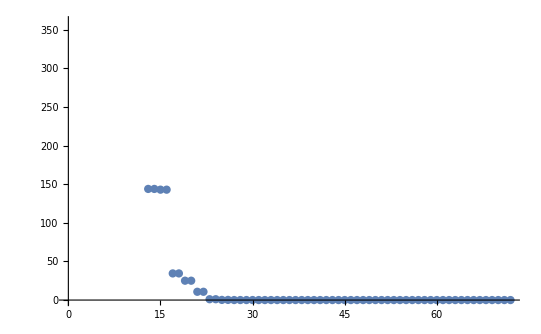

```mathematica
ListPlot[Norm/@Eigenvalues[complexToMat[(M/.nonzeroExpected/.xpOpString[seq__]/;OddQ[Length[{seq}]]->0)]]]
```